Kibble-Zurek Scaling in the Kitaev Model |

Honeycomb Latticepaclet:QuantumMob/QuantumPlaybook/tutorial/KibbleZurekScalingInKitaevModel#1444241214 | Topological Defect Density: Thermodynamic Limitpaclet:QuantumMob/QuantumPlaybook/tutorial/KibbleZurekScalingInKitaevModel#1126481058
Topological Defect Density: Finite Sizepaclet:QuantumMob/QuantumPlaybook/tutorial/KibbleZurekScalingInKitaevModel#928971383 |

Here, the Kibble-Zurek scaling is illustrated for the Kitaev model (Kitaev, 2003). See Sengupta et al. (2008) and Mondal et al. (2008) for details.

Honeycomb Lattice

Set the lattice size:

```mathematica
$L=10;
```

Primitive lattice vectors in the (real-space) honeycomb lattice:

```mathematica
aa={
{1,-Sqrt[3]}*Sqrt[3]/2,
{1,Sqrt[3]}*Sqrt[3]/2
}
```

{{(√3)/2,-3/2},{(√3)/2,3/2}}

Visualize the unit cells in the lattice. Note that each unit cell contains two “atoms” A and B that form the hexagonal lattice:

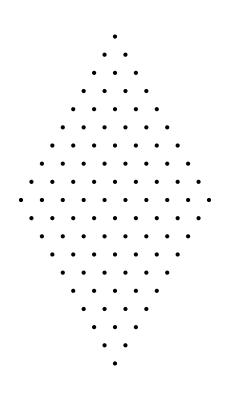

```mathematica
rr=Table[aa[[1]]*r1+aa[[2]]*r2,{r1,0,$L-1},{r2,0,$L-1}];
rr=Map[Point,rr,{2}];
Graphics[rr]
```

The matrix to calculate the cross product in 2D:

```mathematica
RR=RotationMatrix[Pi/2,{0,0,1}][[;;2,;;2]];
```

The area of the unit cell:

```mathematica
A=-aa[[1]].RR.aa[[2]]
```

(3 √3)/2

Get the primitive lattice vectors in the reciprocal lattice (momentum-space lattice):

```mathematica
bb={-RR.aa[[2]],RR.aa[[1]]}*(2Pi/A)
```

{{(2 π)/(√3),-(2 π)/3},{(2 π)/(√3),(2 π)/3}}

The area of the (full) Brillouin zone (i.e., the unit cell in the reciprocal lattice):

```mathematica
B=-bb[[1]].RR.bb[[2]]
```

(8 π^2)/(3 √3)

Check the reciprocal lattice vectors, a_i·b_j=2π δ_ij :

```mathematica
Outer[Dot,aa,bb,1]//MatrixForm
```

(2 π | 0
0 | 2 π)

Visualize the Brillouin zone:

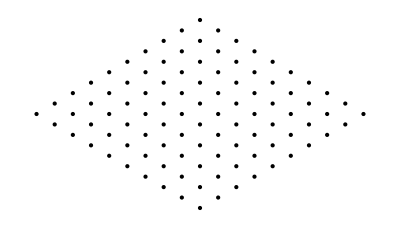

```mathematica
kk=Table[bb[[1]]*k1+bb[[2]]*k2,{k1,0,$L-1},{k2,0,$L-1}]/$L;
kk=Map[Point,kk,{2}];
Graphics[kk]
```

Topological Defect Density: Finite Size

Function top[{n_1,n_2},τ_Q] returns the topological defect density in the Kitaev model on the periodic honeycomb lattice of sizes n_1 and n_2 upon the ramping of J_3(t):=Jt/τ_Q. Note that the sizes n_1 and n_2 are in the direction of the selected primitive lattice vectors a_1 and a_2. It is based on the Landau-Zener estimate in Sengupta et al. (2008) and Mondal et al. (2008).

```mathematica
Clear[top]
top[{n1_,n2_},τ_]:=Module[
{k1,k2,pp},
k1=Range[1,n1-1]*(2Pi/n1);
k2=Range[1,n2-1]*(2Pi/n2);
k1=$J1*Sin[k1];
k2=$J2*Sin[k2];
pp=(2*Pi*τ/$J)*Outer[N[#1-#2]^2&,k1,k2];
Total@Exp[-Flatten@pp]/(n1*n2)
]
```

Set the coupling parameters:

```mathematica
$J1=0.4;
$J2=0.5;
$J=1;
```

Set the scaling variable, which in turns sets the ramping rate parameter τ_Q:

```mathematica
ss=PowerRange[0.01,100,1.5];
ss//Length
```

23

Calculate the defect density:

```mathematica
EchoTiming[
data=Table[
{1/Sqrt[tau],top[{500,n2},tau]},
{n1,100,200,50},
{n2,100,200,50},
{tau,ss^2}
]
];
data=Flatten[data,1];
lgnd=Row[{#[[1]],"×",#[[2]]}]&/@Tuples@{Range[100,200,50],Range[100,200,50]};
```

11.236

Plot the defect density in the log scales:

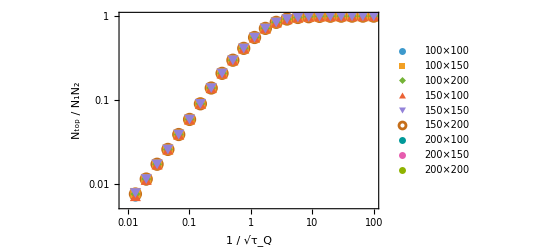

```mathematica
fig1=ListLogLogPlot[data,PlotMarkers->Automatic,
PlotLegends->lgnd,
FrameLabel->{"1 / √τ_Q","N_top / N_1N_2"}]
```

The above result shows that for fast ramp (J τ_Q<1), the system is in the diabatic limit. From now on, we focus on the regime J τ_Q>1.

Calculate the defect density:

```mathematica
ss=PowerRange[1,100,1.25];
ss//Length
EchoTiming[
data=Table[
{1/Sqrt[tau],top[{500,n2},tau]},
{n1,100,200,50},
{n2,100,200,50},
{tau,ss^2}
]
];
data=Flatten[data,1];
lgnd=Row[{#[[1]],"×",#[[2]]}]&/@Tuples@{Range[100,200,50],Range[100,200,50]};
```

21

10.3389

Plot the defect density in the linear scales for small 1/√τ_Q:

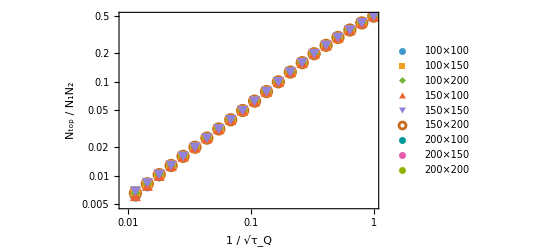

```mathematica
fig2a=ListLogLogPlot[data,PlotMarkers->Automatic,
PlotLegends->lgnd,
FrameLabel->{"1 / √τ_Q","N_top / N_1N_2"}]
```

Re-plot it in the linear scales:

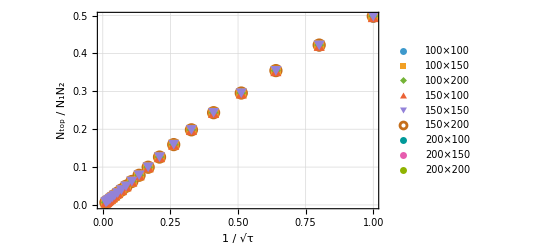

```mathematica
fig2b=ListPlot[data,
PlotMarkers->Automatic,
PlotLegends->lgnd,
FrameLabel->{"1 / √τ","N_top / N_1N_2"}]
```

So, the defect density, N_top/N_1 N_2, is a universal linear function of 1/√τ_Q.

Topological Defect Density: Thermodynamic Limit

Function topInfty[{J_1,J_2},τ_Q] returns the topological defect density in the Kitaev model in the thermodynamic limit. It is based on the same Landau-Zener estimate in Sengupta et al. (2008) and Mondal et al. (2008).

```mathematica
Clear[topInfty]
topInfty[{j1_,j2_},τ_,opts___]:=Module[
{k1,k2},
NIntegrate[
Exp[-2.*Pi*τ*(j1*Sin[k1]-j2*Sin[k2])^2],
{k1,-Pi,Pi},
{k2,-Pi,Pi},
opts,
Method->"LocalAdaptive"
]/(2*Pi)^2
]
```

Calculate the defect density as a function of 1/√τ_Q to see the scaling behavior:

```mathematica
EchoTiming[
dataInfty=Table[
{1/Sqrt[tau],topInfty[{$J1,$J2},tau]},
{tau,ss^2}
]
];
```

2.03266

Plot the topological defect density:

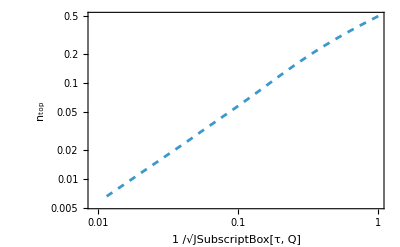

```mathematica
fig3=ListLogLogPlot[dataInfty,
Joined->True,
PlotStyle->Dashed,
FrameLabel->{"1 /√JSubscriptBox[τ, Q]","n_top"}
]
```

Compare the finie-size and thermodynamic-limit resuls:

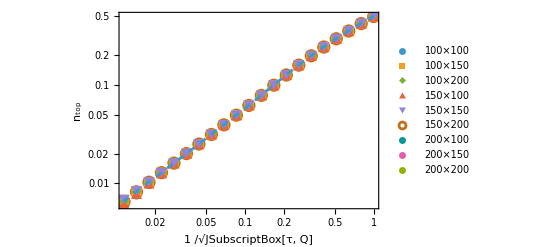

```mathematica
Show[{fig2a,fig3},
PlotRange->All,
FrameLabel->{"1 /√JSubscriptBox[τ, Q]","n_top"}
]
```

Jp[α] returns the parameter pair {J_1,J_2} for α:=tan^-1(J_2/J_1):

```mathematica
Jp[ang_]:={1,Tan[ang]}/(1+Tan[ang])
```

Calculate the defect density as a function of α and τ_Q to reproduce the result in the previously cited works:

```mathematica
EchoTiming[
data=Table[
{t,r,topInfty[Jp[r*Pi],t]},
{t,0.1,10,0.5},
{r,0,0.5,0.025}
]
];
data=Flatten[data,1];
```

15.3475

```mathematica
fig2=ListPlot3D[data,PlotRange->All,
AxesLabel->{"Jτ_Q","ArcTan[J_2/J_1]/π","n_top"}]
```

-Graphics3D-

| Related Guides
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start